## 4N

```mathematica
f[x_]:=1/(1+5 x^2);
```

```mathematica
X=Table[x,{x,-1,1,1/32}];
```

Wartosci funkcji w punktach x odpowiednio od -1 do 1 z krokiem 1/32 wynoszą:

```mathematica
Y=Map[f,X]
```

{1/6,1024/5829,256/1381,1024/5229,64/309,1024/4669,256/1101,1024/4149,16/61,1024/3669,256/861,1024/3229,64/189,1024/2829,256/661,1024/2469,4/9,1024/2149,256/501,1024/1869,64/109,1024/1629,256/381,1024/1429,16/21,1024/1269,256/301,1024/1149,64/69,1024/1069,256/261,1024/1029,1,1024/1029,256/261,1024/1069,64/69,1024/1149,256/301,1024/1269,16/21,1024/1429,256/381,1024/1629,64/109,1024/1869,256/501,1024/2149,4/9,1024/2469,256/661,1024/2829,64/189,1024/3229,256/861,1024/3669,16/61,1024/4149,256/1101,1024/4669,64/309,1024/5229,256/1381,1024/5829,1/6}

```mathematica
XY=Transpose[Distribute[{X,Y}]];
```

```mathematica
Lagrange[XY_]:=Module[{j,k,n,X,Y},
Subscript[X, k_] := Transpose[XY]_⟦1,k+1⟧; 
Subscript[Y, k_] := Transpose[XY]_⟦2,k+1⟧; 
n = Length[XY]-1; 
Return[  ∑_(k=0)^n Subscript[Y, k] ( ∏_(j=0)^(k-1) (x-Subscript[X, j])/(Subscript[X, k]-Subscript[X, j]))(∏_(j=k+1)^n (x-Subscript[X, j])/(Subscript[X, k]-Subscript[X, j])) ];];
```

```mathematica
For[n=2,n≤15,n++,
x1=-1;
x2=1;
XXY=N[Table[{x1+(x2-x1)/n k,f[x1+(x2-x1)/n k]},{k,0,n}]];
Cdot=ListPlot[XY,PlotStyle->{Red,PointSize[0.02]}];
P[x_]=Lagrange[XY];
graph1=Plot[f[x],{x,-2,2},PlotStyle->Green];
graph2=Plot[P[x],{x,-1,1},PlotStyle->Blue];
b=Show[graph1,graph2,Cdot]   ]  ;
```

Wykres wielomianu:
kolor niebieski - wykres wielomianu,
kolor zielony - wykres funkcji,
kolor czerwony - wezly i wartosci funkcji.

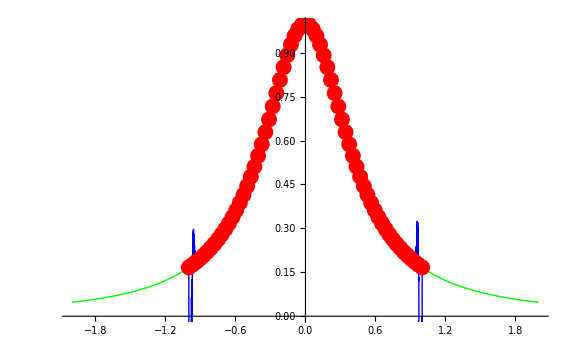

```mathematica
b
```